## The formulae

```mathematica
FindFullFormulaWithPrefix[g_,prefix_]:=Fold [Plus,Map[ChangeSymbol[#,prefix]&,FindFullFormula[g]]]
```

```mathematica
FindFullFormulaWithPrefix[CycleGraph[3],"A"]
```

A1x2x3

```mathematica
NextLetter[l_]:=FromCharacterCode[ToCharacterCode[l]+1]
```

```mathematica
NextLetter["D"]
```

E

```mathematica
CalculateInOutFormulaMany[g_,sets_, prefix_]:=Block[{
currentEdge, 
edges, 
pos,
isInOut, gContract, gRemove, gIn, gOut, result, resIn, resOut, resContract, resRemove, repVertex, in, out,
 contractSets},
If[VertexCount[g]==0,
Interrupt[]
];
(* if there is no set, we have a problem *)
If[Length[sets]==0,
Interrupt[];
];
(* if there is only one set, we are done *)
If[Length[sets]==1,
result=FindFullFormulaWithPrefix[g,prefix];
Return[result];
];

(* there is more than 1 set : we define in to be the first set, out to be thejoin of the rest *)
in=First[sets];
out=Flatten[Rest[sets]];

(* as long as there is an edge between in and out we remove and contract it and recurse *)
edges=EdgeList[g];
For[pos=1,pos <=Length[edges],pos++,
currentEdge=edges[[pos]];
isInOut=MemberQ[in,currentEdge[[1]]]&&MemberQ[out,currentEdge[[2]]];
If[!isInOut,
isInOut=MemberQ[in,currentEdge[[2]]]&&MemberQ[out,currentEdge[[1]]];
currentEdge=UndirectedEdge[currentEdge[[2]],currentEdge[[1]]]
];
If[isInOut,
gContract=GContract[g,currentEdge];
repVertex={currentEdge[[1]]->currentEdge[[2]]};
gContract=Graph[VertexList[gContract]/.repVertex,Map[#[[1]]<->#[[2]]/.repVertex&,EdgeList[gContract]]];
gRemove=EdgeDelete[g,currentEdge];
contractSets=Prepend[Rest[sets],DeleteCases[in,currentEdge[[1]]]];
resContract=CalculateInOutFormulaMany[gContract,contractSets,prefix];
resRemove=CalculateInOutFormulaMany[gRemove,sets,prefix];
result=resRemove-resContract;
Return[result]
];
];

(* there are no more edges between in and out so we compute in and recurse with the rest *)
gIn=Subgraph[g,in];
gOut=Subgraph[g,out];
resIn=If[VertexCount[gIn]==0,1,FindFullFormulaWithPrefix[gIn, prefix]];
resOut=CalculateInOutFormulaMany[gOut,Rest[sets],NextLetter[prefix]];
Return[resIn*resOut]
]
```

```mathematica
CalculateInOutFormulaMany[g_,sets_]:=CalculateInOutFormulaMany[g,sets,"A"]
```

## Now some tests

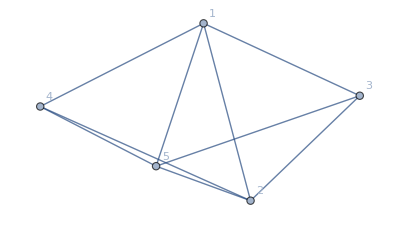

```mathematica
g=Graph[JacobsThalGraph[1],VertexLabels->"Name"]
```

```mathematica
CalculateInOutFormulaMany[g,{{1,2,5},{3},{4}}]
```

18 C4-24 B3 C4+2 A1 B3 C4-A1x2 B3 C4+A1x2x5 B3 C4-A1x5 B3 C4+2 A2 B3 C4-A2x5 B3 C4+2 A5 B3 C4+4 A1 (-C4+B3 C4)-A1x2 (-C4+B3 C4)-A1x5 (-C4+B3 C4)+4 A2 (-C4+B3 C4)-A2x5 (-C4+B3 C4)+4 A5 (-C4+B3 C4)

```mathematica
CollectByPrefix[form_, prefixes_]:=Block[{vars=Select[DeleteDuplicates[ListofVars[form]],StringStartsQ[ SymbolName[#],First[prefixes]]&], rest=Rest[prefixes]},
If[vars=={},
Factor[form],
Total[
Table[
Total[
Map[
If[rest=={},
v*Factor[#],
v*CollectByPrefix[Factor[#],v]
]&
,
CoefficientList[form,v]]
],
{v,Select[vars,SymbolLevel[#]<=4&]}
]
]
]
]
```

```mathematica
CollectByPrefix[18 C4-24 B3 C4+2 A1 B3 C4-A1x2 B3 C4+A1x2x5 B3 C4-A1x5 B3 C4+2 A2 B3 C4-A2x5 B3 C4+2 A5 B3 C4+4 A1 (-C4+B3 C4)-A1x2 (-C4+B3 C4)-A1x5 (-C4+B3 C4)+4 A2 (-C4+B3 C4)-A2x5 (-C4+B3 C4)+4 A5 (-C4+B3 C4),{"A","B"}]
```

A1x2x5 B3 C4-A1x2 (-1+2 B3) C4-A1x5 (-1+2 B3) C4-A2x5 (-1+2 B3) C4+2 A1 (-2+3 B3) C4+2 A2 (-2+3 B3) C4+2 A5 (-2+3 B3) C4+A5 (18-4 A1+A1x2+A1x5-4 A2+A2x5-24 B3+6 A1 B3-2 A1x2 B3+A1x2x5 B3-2 A1x5 B3+6 A2 B3-2 A2x5 B3) C4-A1 (-18-A1x2-A1x5+4 A2-A2x5+4 A5+24 B3+2 A1x2 B3-A1x2x5 B3+2 A1x5 B3-6 A2 B3+2 A2x5 B3-6 A5 B3) C4+A2x5 (18-4 A1+A1x2+A1x5-4 A2-4 A5-24 B3+6 A1 B3-2 A1x2 B3+A1x2x5 B3-2 A1x5 B3+6 A2 B3+6 A5 B3) C4+A2 (18-4 A1+A1x2+A1x5+A2x5-4 A5-24 B3+6 A1 B3-2 A1x2 B3+A1x2x5 B3-2 A1x5 B3-2 A2x5 B3+6 A5 B3) C4+A1x5 (18-4 A1+A1x2-4 A2+A2x5-4 A5-24 B3+6 A1 B3-2 A1x2 B3+A1x2x5 B3+6 A2 B3-2 A2x5 B3+6 A5 B3) C4+A1x2x5 (18-4 A1+A1x2+A1x5-4 A2+A2x5-4 A5-24 B3+6 A1 B3-2 A1x2 B3-2 A1x5 B3+6 A2 B3-2 A2x5 B3+6 A5 B3) C4+A1x2 (18-4 A1+A1x5-4 A2+A2x5-4 A5-24 B3+6 A1 B3+A1x2x5 B3-2 A1x5 B3+6 A2 B3-2 A2x5 B3+6 A5 B3) C4

## Another experiment

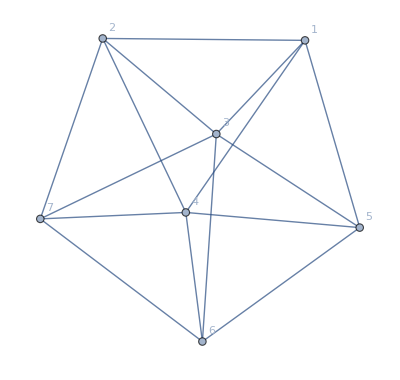

```mathematica
g=Graph[JacobsThalGraph[3],VertexLabels->"Name"]
```

```mathematica
form=CalculateInOutFormulaMany[g,{{1,2,7,6,5},{3},{4}}]
```

210 C4-240 B3 C4+8 A1 B3 C4-4 A1x2 B3 C4+2 (A1x25+A1x2x5) B3 C4-(A16x25+A16x2x5+A1x25x6+A1x26x5+A1x2x5x6) B3 C4+(A16x25x7+A16x2x57+A16x2x5x7+A17x25x6+A17x26x5+A17x2x5x6+A1x25x6x7+A1x26x57+A1x26x5x7+A1x2x57x6+A1x2x5x6x7) B3 C4-(A17x25+A17x2x5+A1x25x7+A1x2x57+A1x2x5x7) B3 C4+(A16x2+A1x26+A1x2x6) B3 C4-(A16x2x7+A17x26+A17x2x6+A1x26x7+A1x2x6x7) B3 C4+2 (A17x2+A1x2x7) B3 C4-4 A1x5 B3 C4+2 (A16x5+A1x5x6) B3 C4-(A16x57+A16x5x7+A17x5x6+A1x57x6+A1x5x6x7) B3 C4+(A17x5+A1x57+A1x5x7) B3 C4-2 (A16+A1x6) B3 C4+(A16x7+A17x6+A1x6x7) B3 C4-2 (A17+A1x7) B3 C4+8 A2 B3 C4-2 (A25+A2x5) B3 C4+(A25x6+A26x5+A2x5x6) B3 C4-(A25x6x7+A26x57+A26x5x7+A2x57x6+A2x5x6x7) B3 C4+(A25x7+A2x57+A2x5x7) B3 C4-2 (A26+A2x6) B3 C4+2 (A26x7+A2x6x7) B3 C4-4 A2x7 B3 C4+8 A5 B3 C4-4 A5x6 B3 C4+2 (A57x6+A5x6x7) B3 C4-2 (A57+A5x7) B3 C4+8 A6 B3 C4-4 A6x7 B3 C4+8 A7 B3 C4+46 A1 (-C4+B3 C4)-14 A1x2 (-C4+B3 C4)+4 (A1x25+A1x2x5) (-C4+B3 C4)-(A16x25+A16x2x5+A1x25x6+A1x26x5+A1x2x5x6) (-C4+B3 C4)-(A17x25+A17x2x5+A1x25x7+A1x2x57+A1x2x5x7) (-C4+B3 C4)+3 (A16x2+A1x26+A1x2x6) (-C4+B3 C4)-(A16x2x7+A17x26+A17x2x6+A1x26x7+A1x2x6x7) (-C4+B3 C4)+4 (A17x2+A1x2x7) (-C4+B3 C4)-14 A1x5 (-C4+B3 C4)+4 (A16x5+A1x5x6) (-C4+B3 C4)-(A16x57+A16x5x7+A17x5x6+A1x57x6+A1x5x6x7) (-C4+B3 C4)+3 (A17x5+A1x57+A1x5x7) (-C4+B3 C4)-10 (A16+A1x6) (-C4+B3 C4)+3 (A16x7+A17x6+A1x6x7) (-C4+B3 C4)-10 (A17+A1x7) (-C4+B3 C4)+46 A2 (-C4+B3 C4)-10 (A25+A2x5) (-C4+B3 C4)+3 (A25x6+A26x5+A2x5x6) (-C4+B3 C4)-(A25x6x7+A26x57+A26x5x7+A2x57x6+A2x5x6x7) (-C4+B3 C4)+3 (A25x7+A2x57+A2x5x7) (-C4+B3 C4)-10 (A26+A2x6) (-C4+B3 C4)+4 (A26x7+A2x6x7) (-C4+B3 C4)-14 A2x7 (-C4+B3 C4)+46 A5 (-C4+B3 C4)-14 A5x6 (-C4+B3 C4)+4 (A57x6+A5x6x7) (-C4+B3 C4)-10 (A57+A5x7) (-C4+B3 C4)+46 A6 (-C4+B3 C4)-14 A6x7 (-C4+B3 C4)+46 A7 (-C4+B3 C4)

```mathematica
CollectByPrefix[form,{"A"}]
```

CollectByPrefix[{A}]

```mathematica
CollectByPrefix[CalculateInOutFormulaMany[g,{{1,2,7,6,5},{3},{4}}],{"A"}]
```

Block[{currentEdge,edges,pos,isInOut,gContract,gRemove,gIn,gOut,result,resIn,resOut,resContract,resRemove,repVertex,in,out,result,contractSets},If[VertexCount[-Graphics-]==0,Interrupt[]];If[Length[{{1,2,7,6,5},{3},{4}}]==0,Interrupt[];];If[Length[{{1,2,7,6,5},{3},{4}}]==1,result=FindFullFormulaWithPrefix[-Graphics-,A];Return[result];];in=First[{{1,2,7,6,5},{3},{4}}];out=Flatten[Rest[{{1,2,7,6,5},{3},{4}}]];edges=EdgeList[-Graphics-];For[pos=1,pos≤Length[edges],pos++,currentEdge=edges⟦pos⟧;isInOut=MemberQ[in,currentEdge⟦1⟧]&&MemberQ[out,currentEdge⟦2⟧];If[!isInOut,isInOut=MemberQ[in,currentEdge⟦2⟧]&&MemberQ[out,currentEdge⟦1⟧];currentEdge=currentEdge⟦2⟧<->currentEdge⟦1⟧];If[isInOut,gContract=GContract[-Graphics-,currentEdge];repVertex={currentEdge⟦1⟧→currentEdge⟦2⟧};gContract=Graph[VertexList[gContract]/.repVertex,(#1⟦1⟧<->#1⟦2⟧/.repVertex&)/@EdgeList[gContract]];gRemove=EdgeDelete[-Graphics-,currentEdge];contractSets=Prepend[Rest[{{1,2,7,6,5},{3},{4}}],DeleteCases[in,currentEdge⟦1⟧]];resContract=CalculateInOutFormulaMany[gContract,contractSets,A];resRemove=CalculateInOutFormulaMany[gRemove,{{1,2,7,6,5},{3},{4}},A];result=resRemove-resContract;Return[result]];];gIn=Subgraph[-Graphics-,in];gOut=Subgraph[-Graphics-,out];resIn=If[VertexCount[gIn]==0,1,FindFullFormulaWithPrefix[gIn,A]];resOut=CalculateInOutFormulaMany[gOut,Rest[{{1,2,7,6,5},{3},{4}}],NextLetter[A]];Return[resIn resOut]]